```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];Needs["EpidCRN`"];Get["HopfE`"];
(*Gavish two-strain model*)(*Test cont with real bdAnalEx outputs*)(*Your setup*)RN={0->"S","S"+"I1"->2*"I1","S"+"Y1"->"Y1"+"I1","I1"->"R1","S"+"I2"->2*"I2","S"+"Y2"->"Y2"+"I2","I2"->"R2","R1"+"I2"->"I2"+"Y2","R1"+"Y2"->2*"Y2","Y2"->"R","R2"+"I1"->"I1"+"Y1","R2"+"Y1"->2*"Y1","Y1"->"R","R1"->"S","R2"->"S","R"->"S","S"->0,"I1"->0,"Y1"->0,"R1"->0,"I2"->0,"Y2"->0,"R2"->0,"R"->0};
rts={La,be1*I1*S,be1*et1*Y1*S,ga1*I1,be2*I2*S,be2*et2*Y2*S,ga2*I2,be2*si2*I2*R1,be2*si2*et2*Y2*R1,ga2*Y2,be1*si1*I1*R2,be1*si1*et1*Y1*R2,ga1*Y1,th1*R1,th2*R2,th3*R,mu*S,mu*I1,mu*Y1,mu*R1,mu*I2,mu*Y2,mu*R2,mu*R};
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
(*Get bdAnalEx outputs*)
{RHS,var,par, cp,mSi,Jx,Jy,E0,ngm,R0,E1,E2,EA,R0A,R12,R21,coP} = bdAnalEx[RN, rts,{1,1,10/4, 3},{7,8,12,13}];
{R01,R02}=R0A/.E0
claP[RHS_,var_,par_,p0val_]:=Module[{conPar,sol,I1val,I2val,tol=10^(-6)},conPar=Thread[par->p0val];
inP=Table[{var[[j]],1/Length[var]},{j,Length[var]}];
sol=Quiet[FindRoot[RHS/. conPar,inP]];
{I1val,I2val}={I1,I2}/. sol;
Print["Classification: I1=",I1val,", I2=",I2val," → ",Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"]];]
p0val=par/.coP;
pos=fpHopf[RHS, var, par, p0val]
```

reactions and transitions: (0→S | La
I1+S→2 I1 | be1 I1 S
S+Y1→I1+Y1 | be1 et1 S Y1
I1→R1 | ga1 I1
I2+S→2 I2 | be2 I2 S
S+Y2→I2+Y2 | be2 et2 S Y2
I2→R2 | ga2 I2
I2+R1→I2+Y2 | be2 I2 R1 si2
R1+Y2→2 Y2 | be2 et2 R1 si2 Y2
Y2→R | ga2 Y2
I1+R2→I1+Y1 | be1 I1 R2 si1
R2+Y1→2 Y1 | be1 et1 R2 si1 Y1
Y1→R | ga1 Y1
R1→S | R1 th1
R2→S | R2 th2
R→S | R th3
S→0 | mu S
I1→0 | I1 mu
Y1→0 | mu Y1
R1→0 | mu R1
I2→0 | I2 mu
Y2→0 | mu Y2
R2→0 | mu R2
R→0 | mu R)

RHS has var {S,I1,Y1,R1,I2,Y2,R2,R} par{be1,be2,et1,et2,ga1,ga2,La,mu,si1,si2,th1,th2,th3}

minimal siphons {{I1,Y1},{I2,Y2}} Check siphon={True,True}

Infection species  at positions: {2,3,5,6}

DFE solution E0: {R→0,R1→0,R2→0,S→La/mu,I1→0,Y1→0,I2→0,Y2→0}

NGM K= ((be1 S)/(ga1+mu) | (be1 et1 S)/(ga1+mu) | 0 | 0
(be1 R2 si1)/(ga1+mu) | (be1 et1 R2 si1)/(ga1+mu) | 0 | 0
0 | 0 | (be2 S)/(ga2+mu) | (be2 et2 S)/(ga2+mu)
0 | 0 | (be2 R1 si2)/(ga2+mu) | (be2 et2 R1 si2)/(ga2+mu)) =((be1 S)/(ga1+mu) | (be1 et1 S)/(ga1+mu) | 0 | 0
0 | 0 | 0 | 0
0 | 0 | (be2 S)/(ga2+mu) | (be2 et2 S)/(ga2+mu)
0 | 0 | 0 | 0)

Reproduction functions R0A: {(be1 (S+et1 R2 si1))/(ga1+mu),(be2 (S+et2 R1 si2))/(ga2+mu)}

R0 at DFE: Max[(be1 S)/(ga1+mu),(be2 S)/(ga2+mu)]

Solve::svars: Equations may not give solutions for all "solve" variables.

Number of boundary systems= 2 ;first sys has 3 sols, E1 is {S→(ga1+mu)/be1,I1→((be1 La-ga1 mu-mu^2) (mu+th1))/(be1 mu (ga1+mu+th1)),Y1→0,R1→(ga1 (be1 La-ga1 mu-mu^2))/(be1 mu (ga1+mu+th1)),R2→0,R→0} second sys has 3 sols, E2 is {S→(ga2+mu)/be2,R1→0,I2→((be2 La-ga2 mu-mu^2) (mu+th2))/(be2 mu (ga2+mu+th2)),Y2→0,R2→(ga2 (be2 La-ga2 mu-mu^2))/(be2 mu (ga2+mu+th2)),R→0}

Fixing parameters at positions: {7,8,12,13} by csi{La→1,mu→1,th2→5/2,th3→3} leaves
{be1,be2,et1,et2,ga1,ga2,si1,si2,th1}

under coP: {be1→3,be2→2,et1→1,et2→1,ga1→1,ga2→1/2,si1→1,si2→1,th1→3/2,La→1,mu→1,th2→5/2,th3→3} invasion nrs are{1.17188,1.01587} repr nrs are{1.5,1.33333}

{(be1 La)/(mu (ga1+mu)),(be2 La)/(mu (ga2+mu))}

{{{0.663902,0.219722,0.00091498,0.086098,0.0230126,0.00298438,0.00276467,0.000601793}},{-2.06166+0.13487 ⅈ,-2.06166-0.13487 ⅈ},-86.2571,{-4.14527,-4.01259,-2.06166+0.13487 ⅈ,-2.06166-0.13487 ⅈ,-1.42768,-1.19605,-1.,-0.0228946}}

Classification: I1=0.219722, I2=0.0230126 → EE

Varying be1 (center=3) and be2 (center=2)

Ranges: be1 ∈ {0,7.}, be2 ∈ {0,4.5}

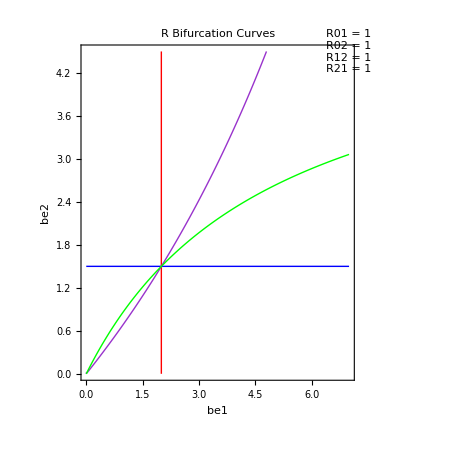

```mathematica
plR[par_,p0val_,plotInd_,R01_,R02_,R12_,R21_,rHei_,rWid_]:=Module[{par1,par2,center1,center2,range1,range2,fixedParams,plots,legendLabels,rCurves,colors,labels},(*Extract the two parameters being varied*)par1=par[[plotInd[[1]]]];
par2=par[[plotInd[[2]]]];
(*Extract their center values*)center1=p0val[[plotInd[[1]]]];
center2=p0val[[plotInd[[2]]]];
(*Define ranges-truncated at 0*)range1={Max[0,center1-rWid/2],center1+rWid/2};
range2={Max[0,center2-rHei/2],center2+rHei/2};
Print["Varying ",par1," (center=",center1,") and ",par2," (center=",center2,")"];
Print["Ranges: ",par1," ∈ ",range1,", ",par2," ∈ ",range2];
(*Create fixed parameter substitution rules*)fInd=Complement[Range[par//Length],plotInd];
fixedParams=Thread[par[[fInd]]->p0val[[fInd]]];
(*Define R curves,colors,and labels*)rCurves={R01,R02,R12,R21};
colors={Red,RGBColor[0,0,1],RGBColor[0.6,0.2,0.8],Green};
labels={"R01 = 1","R02 = 1","R12 = 1","R21 = 1"};
(*Create plots for active R curves*)plots={};
legendLabels={};
activeEquations={};
activeColors={};
activeLabels={};
Do[If[rCurves[[i]]=!=Automatic,AppendTo[activeEquations,Evaluate[(rCurves[[i]]/. fixedParams)==1]];
AppendTo[activeColors,Directive[colors[[i]],Thick]];
AppendTo[activeLabels,Style[labels[[i]],colors[[i]]]];],{i,1,4}];
(*Create single ContourPlot with all equations*)If[Length[activeEquations]>0,plots={ContourPlot[Evaluate[activeEquations],Evaluate[{par1,range1[[1]],range1[[2]]}],Evaluate[{par2,range2[[1]],range2[[2]]}],ContourStyle->activeColors,PlotPoints->50]};
legendLabels=activeLabels;];
(*Create plot object without displaying*)If[Length[plots]>0,Show[plots[[1]],Frame->True,FrameLabel->{ToString[par1],ToString[par2]},PlotLabel->"R Bifurcation Curves",AspectRatio->1,ImageSize->450,PlotRange->{range1,range2},Epilog->{Inset[Framed[Column[legendLabels,Spacings->0.5],Background->White,FrameStyle->Gray,RoundingRadius->5],Scaled[{0.98,0.98}],Scaled[{1,1}]]}],(Print["No R curves to plot."];Graphics[{}])]]

plotInd={1,2};
plot=plR[par,p0val,plotInd,R01,R02,R12,R21,5.0,8.0];plot
```

```mathematica
(*EXECUTE THIS FIRST:*)Clear[scanOsc]

(*Oscillation Detection Analysis-includes detection of oscillatory behavior*)
scanOsc[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,steadyTol_:10^(-5),delta_:1/20,tMax_:200,nInitials_:8,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic,wRan_:1,hRan_:1]:=Block[{stabTol=10^(-8),maxSteps=18000,ndsMethod="StiffnessSwitching",oscTol=10^(-4),bifP1,bifP2,bifP1min,bifP1max,bifP2min,bifP2max,stepSize,bifP1vals,bifP2vals,totalPoints,res,outcomes,outcomeCounts,finalPlot,plotData,betterColors,useGridMode,bifParIdx1,bifParIdx2,bifP1Center,bifP2Center,progressVar,currentProgress,R01F,R02F,R21F,R12F,rCurves,coPForR,numpar,conPar,initialConditions,tsol,finalValues,I1val,I2val,tol,currentType,allSols,uniqueSols,eqType,eqTypes,steadyStateReached,lastValues,deltaCheck,icSet,ic,finalTime,pos,rhsWithParams,rhsWithFunctions,odeSystem,initialCondSystem,I1Index,I2Index,solTol,jacobian,jacobianAtEq,eigenvals,maxRealPart,stabilityType,checkTimes,allCheckValues,maxVariation,isOscillating},(*Define colors with oscillation category*)betterColors={RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[0.8,0.5,0.2],RGBColor[0.6,0.3,0.8],RGBColor[0.9,0.4,0.4],RGBColor[0.7,0.7,0.3],RGBColor[1,1,0],RGBColor[1,0.5,0],RGBColor[0,0.8,0.8],RGBColor[0.8,0,0.8],RGBColor[0.5,0.8,0.5],RGBColor[0.8,0.8,0.5],RGBColor[1.0,0.0,1.0],RGBColor[1,0.6,0.2]};
(*Fixed color mapping including oscillations*)colorMap=<|"DFE"->RGBColor[0,0,1],"E1"->RGBColor[0,1,0],"E2"->RGBColor[0.6,0.2,0.8],"EE-Stable"->RGBColor[1,1,0],"EE-Unstable"->RGBColor[0.9,0.4,0.4],"EE-Marginal"->RGBColor[0.7,0.7,0.3],"Osc"->RGBColor[1,0.6,0.2],"NotGAS"->RGBColor[1,0,0],"E1-E2"->RGBColor[0,0.8,0.8],"EE-E1"->RGBColor[0.8,0,0.8],"EE-E2"->RGBColor[0.5,0.8,0.5],"Multiple"->RGBColor[0.8,0.8,0.5]|>;
(*Compute Jacobian matrix symbolically*)jacobian=D[RHS,{var}];
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract bifurcation parameter indices*)bifParIdx1=First[plotInd];
bifParIdx2=Last[plotInd];
bifP1Center=Part[p0val,bifParIdx1];
bifP2Center=Part[p0val,bifParIdx2];
If[useGridMode,(*GRID MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1min+(bifP1max-bifP1min)*k/(gridRes-1),{k,0,gridRes-1}];
bifP2vals=Table[bifP2min+(bifP2max-bifP2min)*k/(gridRes-1),{k,0,gridRes-1}];,(*RANGE MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1,{bifP1,bifP1min,bifP1max,delta}];
bifP2vals=Table[bifP2,{bifP2,bifP2min,bifP2max,delta}];];
totalPoints=Length[bifP1vals]*Length[bifP2vals];
(*Initialize for time series scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);
(*Create diverse initial condition sets*)initialConditions={};
(*Set 1:DFE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 2:E1-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 3:E2-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Set 4:EE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Additional random initial conditions*)Do[icSet=Table[RandomReal[{0.001,0.2}],{Length[var]}];
AppendTo[initialConditions,icSet];,{nInitials-4}];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[bifParIdx1]]=bifP1;
numpar[[bifParIdx2]]=bifP2;
conPar=Thread[par->numpar];
(*Substitute parameters in RHS*)rhsWithParams=RHS/. conPar;
rhsWithFunctions=rhsWithParams/. Thread[var->Through[var[t]]];
(*Run time series from different initial conditions*)allSols={};
Do[ic=initialConditions[[k]];
odeSystem=MapThread[#1'[t]==#2&,{var,rhsWithFunctions}];
initialCondSystem=MapThread[#1[0]==#2&,{var,ic}];
tsol=Quiet[NDSolve[Join[odeSystem,initialCondSystem],var,{t,0,tMax},Method->ndsMethod,MaxSteps->maxSteps]];
If[Length[tsol]>0&&tsol[[1]]=!=$Failed,finalValues=Table[var[[j]][tMax]/. tsol[[1]],{j,1,Length[var]}];
(*Enhanced oscillation detection*)checkTimes=Table[0.8*tMax+0.2*tMax*i/10,{i,0,10}];
allCheckValues=Table[Table[var[[j]][t]/. tsol[[1]],{j,1,Length[var]}],{t,checkTimes}];
maxVariation=Max[StandardDeviation/@Transpose[allCheckValues]];
(*Classify behavior*)isOscillating=(maxVariation>oscTol);
finalTime=0.9*tMax;
lastValues=Table[var[[j]][finalTime]/. tsol[[1]],{j,1,Length[var]}];
deltaCheck=Max[Abs[finalValues-lastValues]];
steadyStateReached=(deltaCheck<steadyTol);
If[AllTrue[finalValues,#>=0&],If[isOscillating,AppendTo[allSols,{"Osc",finalValues}],If[steadyStateReached,AppendTo[allSols,finalValues]]]];];,{k,1,Length[initialConditions]}];
If[Length[allSols]>0,(*Check for oscillations first*)oscillatingSols=Select[allSols,ListQ[#]&&Length[#]==2&&#[[1]]=="Osc"&];
steadySols=Select[allSols,!ListQ[#]||(ListQ[#]&&#[[1]]!="Osc")&];
If[Length[oscillatingSols]>0,(*Found oscillations*)currentType="Osc";,(*No oscillations,check steady states*)If[Length[steadySols]>0,(*Find unique attractors*)uniqueSols={steadySols[[1]]};
Do[If[Min[Table[Max[Abs[steadySols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,steadySols[[i]]]];,{i,2,Length[steadySols]}];
(*Classify equilibria with stability analysis for EE*)If[Length[uniqueSols]>1,eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
(*For EE points,analyze stability*)If[eqType=="EE",jacobianAtEq=jacobian/. Thread[var->uniqueSols[[k]]]/. conPar;
eigenvals=Quiet[Eigenvalues[N[jacobianAtEq]]];
If[Length[eigenvals]>0&&FreeQ[eigenvals,_Eigenvalues],maxRealPart=Max[Re[eigenvals]];
stabilityType=Which[maxRealPart<-stabTol,"EE-Stable",maxRealPart>stabTol,"EE-Unstable",True,"EE-Marginal"];
eqType=stabilityType;];];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
eqTypes=Sort[DeleteDuplicates[eqTypes]];
currentType=Which[Length[eqTypes]==1,eqTypes[[1]],ContainsAny[eqTypes,{"EE-Stable","EE-Unstable","EE-Marginal"}]&&ContainsAll[eqTypes,{"E1"}],"EE-E1",ContainsAny[eqTypes,{"EE-Stable","EE-Unstable","EE-Marginal"}]&&ContainsAll[eqTypes,{"E2"}],"EE-E2",ContainsAll[eqTypes,{"E1","E2"}],"E1-E2",True,"Multiple"];,(*Single attractor-analyze stability if EE*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
(*For EE,determine stability*)If[currentType=="EE",jacobianAtEq=jacobian/. Thread[var->uniqueSols[[1]]]/. conPar;
eigenvals=Quiet[Eigenvalues[N[jacobianAtEq]]];
If[Length[eigenvals]>0&&FreeQ[eigenvals,_Eigenvalues],maxRealPart=Max[Re[eigenvals]];
currentType=Which[maxRealPart<-stabTol,"EE-Stable",maxRealPart>stabTol,"EE-Unstable",True,"EE-Marginal"];];];];,(*No steady solutions found*)currentType="NotGAS";];];
res=Append[res,{N[bifP1],N[bifP2],currentType}];,(*No solutions found*)res=Append[res,{N[bifP1],N[bifP2],"NotGAS"}];];,{bifP2,bifP2vals}];,{bifP1,bifP1vals}];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
(*Create plot with fixed colors*)plotData=Table[Select[res,#[[3]]==outcomes[[i]]&][[All,1;;2]],{i,1,Length[outcomes]}];
plotMarkers=Table[{Style["●",colorMap[outcomes[[i]]]],14},{i,1,Length[outcomes]}];
finalPlot=ListPlot[plotData,PlotMarkers->plotMarkers,PlotLegends->outcomes,AspectRatio->1,PlotRange->{{bifP1min,bifP1max},{bifP2min,bifP2max}}];
(*Add original plot if provided*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot]];
(*Simple summary with percentages*)Do[Print[outcomes[[i]],": ",outcomeCounts[[i]]," (",Round[100.*outcomeCounts[[i]]/Length[res]],"%)"],{i,1,Length[outcomes]}];
(*Return separated point types*)unClassifPoints=Select[res,#[[3]]=="NotGAS"&];
oscPoints=Select[res,#[[3]]=="Osc"&];
{finalPlot,unClassifPoints,oscPoints,res}];
```

DFE: 62 (5%)

NotGAS: 400 (33%)

E2: 242 (20%)

Osc: 24 (2%)

E1: 313 (26%)

EE-Stable: 184 (15%)

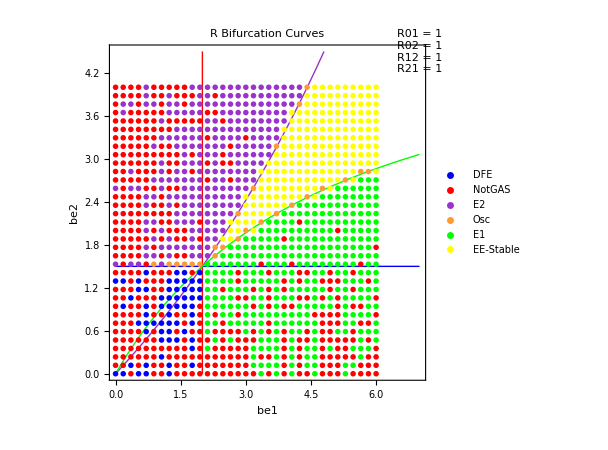

```mathematica
plotInd={1,2};tMax=300;nIc=8;stTol=10^(-4);
{fPl,unC,oscP,res}=scanOsc[RHS,var,par,p0val,plotInd,35,plot,1/20,tMax,nIc,stTol];fPl
```

```mathematica
oscP
```

{{0.883206,1.53003,Osc},{1.23609,1.53003,Osc},{1.41253,1.53003,Osc},{1.58897,1.53003,Osc},{1.76541,1.53003,Osc},{1.94185,1.53003,Osc},{2.29474,1.64765,Osc},{2.29474,1.76526,Osc},{2.47118,1.76526,Osc},{2.82406,1.88288,Osc},{2.82406,2.23574,Osc},{3.0005,2.0005,Osc},{3.17694,2.58859,Osc},{3.35338,2.11812,Osc},{3.70626,2.23574,Osc},{3.70626,3.17668,Osc},{4.05915,2.35335,Osc},{4.23559,3.76476,Osc},{4.41203,2.47097,Osc},{4.41203,4.,Osc},{4.76491,2.58859,Osc},{5.29424,2.70621,Osc},{5.64712,2.82382,Osc},{5.82356,2.82382,Osc}}

```mathematica
(*EXECUTE THIS FIRST:*)Clear[scanEESta]

(*EE Stability Analysis-splits EE category by local stability*)
scanEESta[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,delta_:1/20,tMax_:200,nInitials_:8,steadyTol_:10^(-5),R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic,wRan_:1,hRan_:1]:=Block[{stabTol=10^(-8),maxSteps=18000,ndsMethod="StiffnessSwitching",bifP1,bifP2,bifP1min,bifP1max,bifP2min,bifP2max,stepSize,bifP1vals,bifP2vals,totalPoints,res,outcomes,outcomeCounts,finalPlot,plotData,betterColors,useGridMode,bifParIdx1,bifParIdx2,bifP1Center,bifP2Center,progressVar,currentProgress,R01F,R02F,R21F,R12F,rCurves,coPForR,numpar,conPar,initialConditions,tsol,finalValues,I1val,I2val,tol,currentType,allSols,uniqueSols,eqType,eqTypes,steadyStateReached,lastValues,deltaCheck,icSet,ic,finalTime,pos,rhsWithParams,rhsWithFunctions,odeSystem,initialCondSystem,I1Index,I2Index,solTol,jacobian,jacobianAtEq,eigenvals,maxRealPart,stabilityType},(*Define colors-expanded for stability subcategories*)betterColors={RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[0.8,0.5,0.2],RGBColor[0.6,0.3,0.8],(*EE-Stable:dark purple*)RGBColor[0.9,0.4,0.4],(*EE-Unstable:red*)RGBColor[0.7,0.7,0.3],(*EE-Marginal:olive*)RGBColor[1,1,0],RGBColor[1,0.5,0],RGBColor[0,0.8,0.8],RGBColor[0.8,0,0.8],RGBColor[0.5,0.8,0.5],RGBColor[0.8,0.8,0.5],RGBColor[1.0,0.0,1.0]};
(*Compute Jacobian matrix symbolically*)jacobian=D[RHS,{var}];
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract bifurcation parameter indices*)bifParIdx1=First[plotInd];
bifParIdx2=Last[plotInd];
bifP1Center=Part[p0val,bifParIdx1];
bifP2Center=Part[p0val,bifParIdx2];
If[useGridMode,(*GRID MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1min+(bifP1max-bifP1min)*k/(gridRes-1),{k,0,gridRes-1}];
bifP2vals=Table[bifP2min+(bifP2max-bifP2min)*k/(gridRes-1),{k,0,gridRes-1}];,(*RANGE MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1,{bifP1,bifP1min,bifP1max,delta}];
bifP2vals=Table[bifP2,{bifP2,bifP2min,bifP2max,delta}];];
totalPoints=Length[bifP1vals]*Length[bifP2vals];
(*Initialize for time series scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);
(*Create diverse initial condition sets*)initialConditions={};
(*Set 1:DFE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 2:E1-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 3:E2-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Set 4:EE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Additional random initial conditions*)Do[icSet=Table[RandomReal[{0.001,0.2}],{Length[var]}];
AppendTo[initialConditions,icSet];,{nInitials-4}];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[bifParIdx1]]=bifP1;
numpar[[bifParIdx2]]=bifP2;
conPar=Thread[par->numpar];
(*Substitute parameters in RHS*)rhsWithParams=RHS/. conPar;
rhsWithFunctions=rhsWithParams/. Thread[var->Through[var[t]]];
(*Run time series from different initial conditions*)allSols={};
Do[ic=initialConditions[[k]];
odeSystem=MapThread[#1'[t]==#2&,{var,rhsWithFunctions}];
initialCondSystem=MapThread[#1[0]==#2&,{var,ic}];
tsol=Quiet[NDSolve[Join[odeSystem,initialCondSystem],var,{t,0,tMax},Method->ndsMethod,MaxSteps->maxSteps]];
If[Length[tsol]>0&&tsol[[1]]=!=$Failed,finalValues=Table[var[[j]][tMax]/. tsol[[1]],{j,1,Length[var]}];
finalTime=0.9*tMax;
lastValues=Table[var[[j]][finalTime]/. tsol[[1]],{j,1,Length[var]}];
deltaCheck=Max[Abs[finalValues-lastValues]];
steadyStateReached=(deltaCheck<steadyTol);
If[steadyStateReached&&AllTrue[finalValues,#>=0&],AppendTo[allSols,finalValues]];];,{k,1,Length[initialConditions]}];
If[Length[allSols]>0,(*Find unique attractors*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify equilibria with stability analysis for EE*)If[Length[uniqueSols]>1,eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
(*For EE points,analyze stability*)If[eqType=="EE",jacobianAtEq=jacobian/. Thread[var->uniqueSols[[k]]]/. conPar;
eigenvals=Quiet[Eigenvalues[N[jacobianAtEq]]];
If[Length[eigenvals]>0&&FreeQ[eigenvals,_Eigenvalues],maxRealPart=Max[Re[eigenvals]];
stabilityType=Which[maxRealPart<-stabTol,"EE-Stable",maxRealPart>stabTol,"EE-Unstable",True,"EE-Marginal"];
eqType=stabilityType;];];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
eqTypes=Sort[DeleteDuplicates[eqTypes]];
currentType=Which[Length[eqTypes]==1,eqTypes[[1]],ContainsAny[eqTypes,{"EE-Stable","EE-Unstable","EE-Marginal"}]&&ContainsAll[eqTypes,{"E1"}],"EE-E1",ContainsAny[eqTypes,{"EE-Stable","EE-Unstable","EE-Marginal"}]&&ContainsAll[eqTypes,{"E2"}],"EE-E2",ContainsAll[eqTypes,{"E1","E2"}],"E1-E2",True,"Multiple"];,(*Single attractor-analyze stability if EE*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
(*For EE,determine stability*)If[currentType=="EE",jacobianAtEq=jacobian/. Thread[var->uniqueSols[[1]]]/. conPar;
eigenvals=Quiet[Eigenvalues[N[jacobianAtEq]]];
If[Length[eigenvals]>0&&FreeQ[eigenvals,_Eigenvalues],maxRealPart=Max[Re[eigenvals]];
currentType=Which[maxRealPart<-stabTol,"EE-Stable",maxRealPart>stabTol,"EE-Unstable",True,"EE-Marginal"];];];];
res=Append[res,{N[bifP1],N[bifP2],currentType}];,(*No solutions found*)res=Append[res,{N[bifP1],N[bifP2],"NotGAS"}];];,{bifP2,bifP2vals}];,{bifP1,bifP1vals}];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
(*Create simple plot*)plotData=Table[Select[res,#[[3]]==outcomes[[i]]&][[All,1;;2]],{i,1,Length[outcomes]}];
finalPlot=ListPlot[plotData,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->outcomes,AspectRatio->1,PlotRange->{{bifP1min,bifP1max},{bifP2min,bifP2max}}];
(*Add original plot if provided*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot]];
(*Simple summary with percentages*)Do[Print[outcomes[[i]],": ",outcomeCounts[[i]]," (",Round[100.*outcomeCounts[[i]]/Length[res]],"%)"],{i,1,Length[outcomes]}];
(*Return NotGAS points as errors*)unClassifPoints=Select[res,#[[3]]=="NotGAS"&];
{finalPlot,unClassifPoints,res}];
```

NotGAS: 351 (29%)

DFE: 42 (3%)

E2: 254 (21%)

E1: 316 (26%)

EE-Stable: 262 (21%)

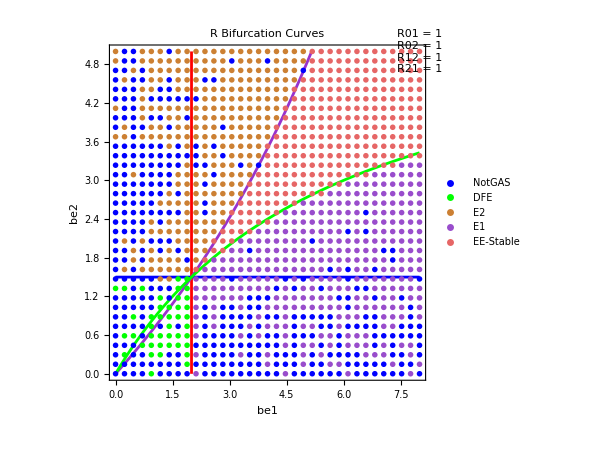

```mathematica
plotInd={1,2};tMax=300;nIc=8;stTol=10^(-4);
{fPl,noG,res}=scanEESta[RHS,var,par,p0val,plotInd,35,plot,1/20,tMax,nIc,stTol];fPl
```

NotGAS: 365 (30%)

DFE: 38 (3%)

E2: 248 (20%)

E1: 310 (25%)

EE-Stable: 264 (22%)

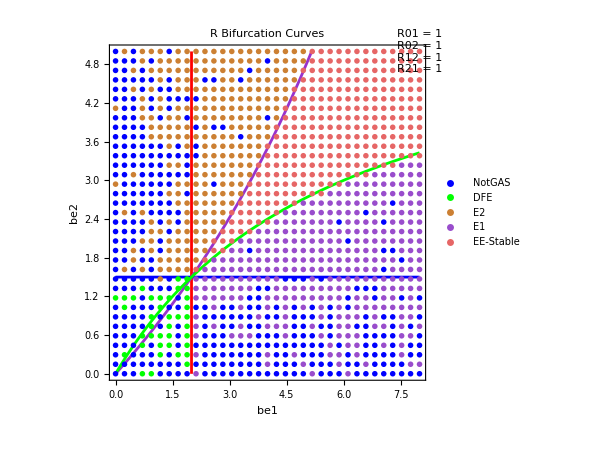

```mathematica
plotInd={1,2};tMax=300;nIc=8;stTol=10^(-3);
{fPl,noG,res}=scanEESta[RHS,var,par,p0val,plotInd,35,plot,0.01,1/30,tMax,nIc,stTol];fPl
```

```mathematica
Clear[scan4TS]

(*Simplified Time Series Simulation-based multiple equilibrium scanning*)
scan4TS[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic,tMax_:100,nInitials_:8,steadyTol_:10^(-6)]:=Block[{bifP1,bifP2,bifP1min,bifP1max,bifP2min,bifP2max,stepSize,bifP1vals,bifP2vals,totalPoints,res,outcomes,outcomeCounts,finalPlot,plotData,betterColors,useGridMode,bifParIdx1,bifParIdx2,bifP1Center,bifP2Center,progressVar,currentProgress,R01F,R02F,R21F,R12F,rCurves,coPForR,numpar,conPar,initialConditions,tsol,finalValues,I1val,I2val,tol,currentType,allSols,uniqueSols,eqType,eqTypes,steadyStateReached,lastValues,deltaCheck,icSet,ic,finalTime,pos,rhsWithParams,rhsWithFunctions,odeSystem,initialCondSystem,I1Index,I2Index,solTol},(*Define colors*)betterColors={RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[0.8,0.5,0.2],RGBColor[0.6,0.3,0.8],RGBColor[1,1,0],RGBColor[1,0.5,0],RGBColor[0,0.8,0.8],RGBColor[0.8,0,0.8],RGBColor[0.5,0.8,0.5],RGBColor[0.8,0.8,0.5],RGBColor[1.0,0.0,1.0]};
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract bifurcation parameter indices*)bifParIdx1=First[plotInd];
bifParIdx2=Last[plotInd];
bifP1Center=Part[p0val,bifParIdx1];
bifP2Center=Part[p0val,bifParIdx2];
If[useGridMode,(*GRID MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1min+(bifP1max-bifP1min)*k/(gridRes-1),{k,0,gridRes-1}];
bifP2vals=Table[bifP2min+(bifP2max-bifP2min)*k/(gridRes-1),{k,0,gridRes-1}];,(*RANGE MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1,{bifP1,bifP1min,bifP1max,delta}];
bifP2vals=Table[bifP2,{bifP2,bifP2min,bifP2max,delta}];];
totalPoints=Length[bifP1vals]*Length[bifP2vals];
(*Initialize for time series scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);
(*Create diverse initial condition sets*)initialConditions={};
(*Set 1:DFE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 2:E1-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 3:E2-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Set 4:EE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Additional random initial conditions*)Do[icSet=Table[RandomReal[{0.001,0.2}],{Length[var]}];
AppendTo[initialConditions,icSet];,{nInitials-4}];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[bifParIdx1]]=bifP1;
numpar[[bifParIdx2]]=bifP2;
conPar=Thread[par->numpar];
(*Substitute parameters in RHS*)rhsWithParams=RHS/. conPar;
rhsWithFunctions=rhsWithParams/. Thread[var->Through[var[t]]];
(*Run time series from different initial conditions*)allSols={};
Do[ic=initialConditions[[k]];
odeSystem=MapThread[#1'[t]==#2&,{var,rhsWithFunctions}];
initialCondSystem=MapThread[#1[0]==#2&,{var,ic}];
tsol=Quiet[NDSolve[Join[odeSystem,initialCondSystem],var,{t,0,tMax}]];
If[Length[tsol]>0&&tsol[[1]]=!=$Failed,finalValues=Table[var[[j]][tMax]/. tsol[[1]],{j,1,Length[var]}];
finalTime=0.9*tMax;
lastValues=Table[var[[j]][finalTime]/. tsol[[1]],{j,1,Length[var]}];
deltaCheck=Max[Abs[finalValues-lastValues]];
steadyStateReached=(deltaCheck<steadyTol);
If[steadyStateReached&&AllTrue[finalValues,#>=0&],AppendTo[allSols,finalValues]];];,{k,1,Length[initialConditions]}];
If[Length[allSols]>0,(*Find unique attractors*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify equilibria*)If[Length[uniqueSols]>1,eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
eqTypes=Sort[DeleteDuplicates[eqTypes]];
currentType=Which[ContainsAll[eqTypes,{"EE","E1"}]&&Length[eqTypes]==2,"EE-E1",ContainsAll[eqTypes,{"EE","E2"}]&&Length[eqTypes]==2,"EE-E2",ContainsAll[eqTypes,{"E1","E2"}]&&Length[eqTypes]==2,"E1-E2",True,"Multiple"];,(*Single attractor*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];];
res=Append[res,{N[bifP1],N[bifP2],currentType}];,(*No solutions found*)res=Append[res,{N[bifP1],N[bifP2],"NotGAS"}];];,{bifP2,bifP2vals}];,{bifP1,bifP1vals}];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
(*Create simple plot*)plotData=Table[Select[res,#[[3]]==outcomes[[i]]&][[All,1;;2]],{i,1,Length[outcomes]}];
finalPlot=ListPlot[plotData,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->outcomes,AspectRatio->1,PlotRange->{{bifP1min,bifP1max},{bifP2min,bifP2max}}];
(*Add original plot if provided*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot]];
(*Simple summary*)Do[Print[outcomes[[i]],": ",outcomeCounts[[i]]," (",Round[100.*outcomeCounts[[i]]/Length[res]],"%)"],{i,1,Length[outcomes]}];
(*Return NotGAS points as errors*)unClassifPoints=Select[res,#[[3]]=="NotGAS"&];
{finalPlot,unClassifPoints,res}];
```

DFE: 42 (3%)

NotGAS: 211 (17%)

E2: 341 (28%)

E1: 440 (36%)

EE: 191 (16%)

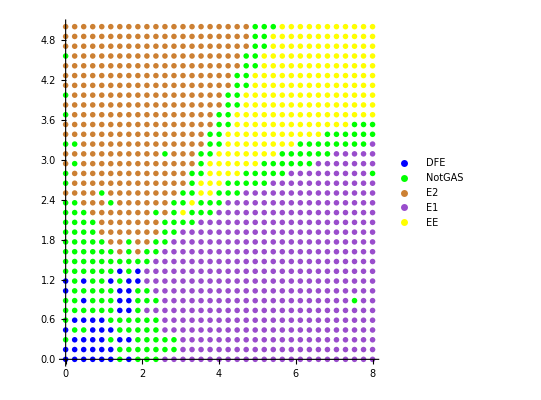

```mathematica
plotInd={1,2};
{fPl,noS,res}=scan4TS[RHS,var,par,p0val,plotInd,35,Automatic,0.01,1/20,1.0,1.0,R01,R02,R21,R12,100,8,10^(-6)];fPl
```

DFE: 48 (4%)

NotGAS: 149 (12%)

E2: 356 (29%)

E1: 453 (37%)

EE: 219 (18%)

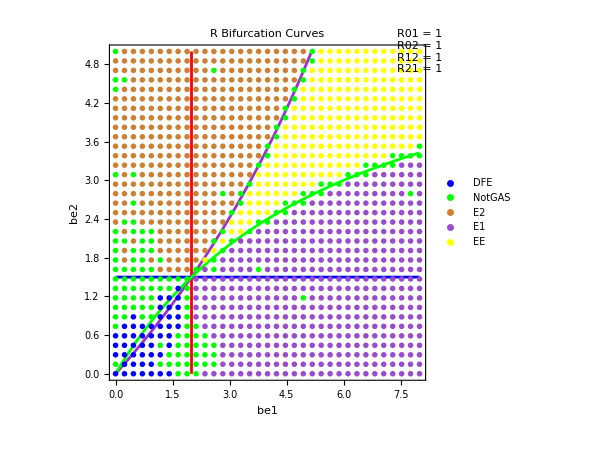

```mathematica
tMax=200;nIc=8;{fPl,noS,res}=scan4TS[RHS,var,par,p0val,plotInd,35,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12,tMax,nIc,10^(-6)];fPl
```

I1 at index 2, I2 at index 5

Varying parameters at indices {1,2} with center values: {4,5/2}

Using grid mode with 60×60 points...

Total points to scan: 3600

Initial conditions created

Scanning complete!

Found equilibrium types: {DFE (270 points),E2 (919 points),E1 (1291 points),EE (236 points),E1-E2 (344 points),error (18 points),EE-E2 (88 points),EE-E1 (213 points),Coexist (221 points)}

Including 18 errors

Summary:

DFE | 270 | 8%
E2 | 919 | 26%
E1 | 1291 | 36%
EE | 236 | 7%
E1-E2 | 344 | 10%
error | 18 | 0%
EE-E2 | 88 | 2%
EE-E1 | 213 | 6%
Coexist | 221 | 6%

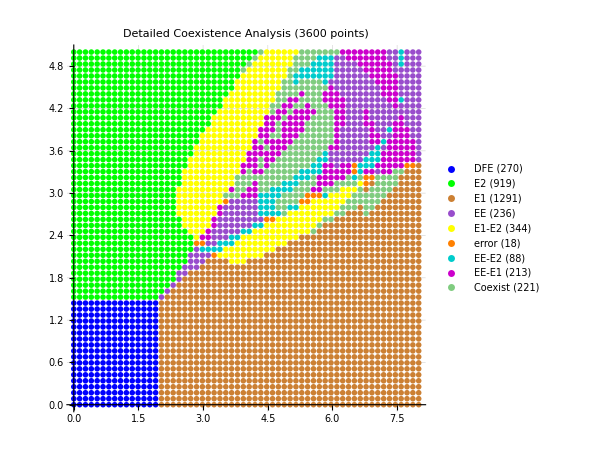

Varying be1 (center=4) and be2 (center=5/2)

Ranges: be1 ∈ {0.,8.}, be2 ∈ {0.,5.}

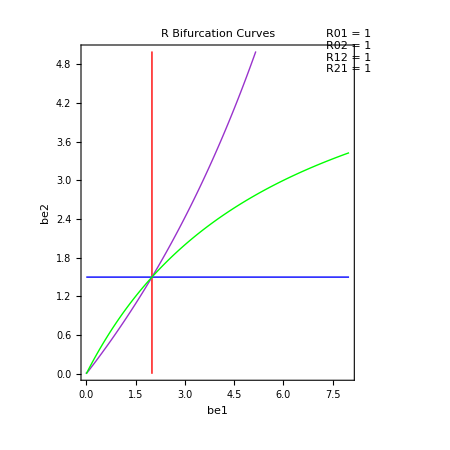

```mathematica
(*Multiple equilibrium scanning with coexistence detection*)scan4[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic]:=Module[{(*Parameter ranges and scanning*)β1,β2,β1min,β1max,β2min,β2max,stepSize,β1vals,β2vals,totalPoints,(*Results collection*)res,outcomes,outcomeCounts,(*Plotting and visualization*)finalPlot,plotData,betterColors,simpleTooltips,(*Mode detection*)useGridMode,β1Index,β2Index,β1Center,β2Center,(*Progress tracking*)progressVar,currentProgress,(*R curve variables*)R01F,R02F,R21F,R12F,rCurves,coPForR,(*Multiple equilibrium variables*)numpar,conPar,inP,in0,in1,in2,sol0,sol1,sol2,solMain,I1val,I2val,tol,currentType,errors,gridResults,nB1,nB2,(*Index finding*)I1Index,I2Index,solTol,allSols,uniqueSols,eqType,eqTypes},(*Define colors including detailed coexistence categories*)betterColors={RGBColor[0,0,1],(*Pure Blue for DFE*)RGBColor[0,1,0],(*Pure Green for E1*)RGBColor[0.8,0.5,0.2],(*Orange for E2*)RGBColor[0.6,0.3,0.8],(*Purple for EE*)RGBColor[1,1,0],(*Yellow for EE-E1*)RGBColor[1,0.5,0],(*Red-Orange for EE-E2*)RGBColor[0,0.8,0.8],(*Cyan for E1-E2*)RGBColor[0.8,0,0.8],(*Magenta for EE-DFE*)RGBColor[0.5,0.8,0.5],(*Light Green for E1-DFE*)RGBColor[0.8,0.8,0.5],(*Light Orange for E2-DFE*)RGBColor[1.0,0.0,1.0](*Magenta for errors/NoSol*)};
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
Print["I1 at index ",I1Index,", I2 at index ",I2Index];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract parameter indices*)β1Index=If[Length[plotInd]>=1,plotInd[[1]],1];
β2Index=If[Length[plotInd]>=2,plotInd[[2]],2];
β1Center=p0val[[β1Index]];
β2Center=p0val[[β2Index]];
Print["Varying parameters at indices ",{β1Index,β2Index}," with center values: ",{β1Center,β2Center}];
If[useGridMode,(*GRID MODE*)Print["Using grid mode with ",gridRes,"×",gridRes," points..."];
β1min=Max[β1Center*(1-wRan),0.001];
β1max=β1Center*(1+wRan);
β2min=Max[β2Center*(1-hRan),0.001];
β2max=β2Center*(1+hRan);
β1vals=Table[β1min+(β1max-β1min)*k/(gridRes-1),{k,0,gridRes-1}];
β2vals=Table[β2min+(β2max-β2min)*k/(gridRes-1),{k,0,gridRes-1}];
stepSize="grid";,(*RANGE MODE*)Print["Using range mode with step size ",delta,"..."];
β1min=Max[β1Center*(1-wRan),0.001];
β1max=β1Center*(1+wRan);
β2min=Max[β2Center*(1-hRan),0.001];
β2max=β2Center*(1+hRan);
β1vals=Table[β1,{β1,β1min,β1max,delta}];
β2vals=Table[β2,{β2,β2min,β2max,delta}];
stepSize=delta;];
(*R curve preparation*)rCurves={};
If[R01=!=Automatic||R02=!=Automatic||R21=!=Automatic||R12=!=Automatic,coPForR=Thread[par->p0val];
coPForR=DeleteCases[coPForR,HoldPattern[par[[β1Index]]->_]|HoldPattern[par[[β2Index]]->_]];
If[R01=!=Automatic,R01F=R01/. coPForR;
AppendTo[rCurves,ContourPlot[R01F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Red,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R02=!=Automatic,R02F=R02/. coPForR;
AppendTo[rCurves,ContourPlot[R02F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Blue,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R21=!=Automatic,R21F=R21/. coPForR;
AppendTo[rCurves,ContourPlot[R21F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Green,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R12=!=Automatic,R12F=R12/. coPForR;
AppendTo[rCurves,ContourPlot[R12F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Orange,Thick,Opacity[0.8]],PlotPoints->30]]];];
totalPoints=Length[β1vals]*Length[β2vals];
Print["Total points to scan: ",totalPoints];
(*Initialize for multiple equilibrium scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);(*Tolerance for comparing solutions*)(*Create initial condition arrays*)inP=Table[{var[[j]],1/Length[var]},{j,Length[var]}];(*General initial*)in0=inP;in0[[I1Index,2]]=0;in0[[I2Index,2]]=0;(*DFE:I1=I2=0*)in1=inP;in1[[I2Index,2]]=0;(*E1:I2=0*)in2=inP;in2[[I1Index,2]]=0;(*E2:I1=0*)Print["Initial conditions created"];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP WITH 4 EQUILIBRIUM SEARCHES*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[β1Index]]=β1;
numpar[[β2Index]]=β2;
conPar=Thread[par->numpar];
(*Four FindRoot calls with different initial conditions*)solMain=Quiet[FindRoot[RHS/. conPar,inP]];(*General*)sol0=Quiet[FindRoot[RHS/. conPar,in0]];(*DFE-like*)sol1=Quiet[FindRoot[RHS/. conPar,in1]];(*E1-like*)sol2=Quiet[FindRoot[RHS/. conPar,in2]];(*E2-like*)(*Collect all successful solutions*)allSols={};
If[Head[solMain]===List,AppendTo[allSols,var/. solMain]];
If[Head[sol0]===List,AppendTo[allSols,var/. sol0]];
If[Head[sol1]===List,AppendTo[allSols,var/. sol1]];
If[Head[sol2]===List,AppendTo[allSols,var/. sol2]];
If[Length[allSols]>0,(*Find unique solutions (within tolerance)*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify based on number of unique equilibria*)If[Length[uniqueSols]>1,(*Multiple equilibria-classify each and determine coexistence type*)eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
(*Remove duplicates and sort to get consistent naming*)eqTypes=Sort[DeleteDuplicates[eqTypes]];
(*Determine coexistence type*)currentType=Which[ContainsAll[eqTypes,{"EE","E1"}]&&Length[eqTypes]==2,"EE-E1",ContainsAll[eqTypes,{"EE","E2"}]&&Length[eqTypes]==2,"EE-E2",ContainsAll[eqTypes,{"E1","E2"}]&&Length[eqTypes]==2,"E1-E2",ContainsAll[eqTypes,{"EE","DFE"}]&&Length[eqTypes]==2,"EE-DFE",ContainsAll[eqTypes,{"E1","DFE"}]&&Length[eqTypes]==2,"E1-DFE",ContainsAll[eqTypes,{"E2","DFE"}]&&Length[eqTypes]==2,"E2-DFE",True,"Coexist" (*For 3+types or unexpected combinations*)];,(*Single equilibrium-classify by I1,I2 values*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];];
res=Append[res,{N[β1],N[β2],currentType}];,(*All FindRoot calls failed*)res=Append[res,{N[β1],N[β2],"NoSol"}];];,{β2,β2vals}];,{β1,β1vals}];
Print["Scanning complete!"];
(*Simple error detection for grid mode*)errors={};
If[useGridMode&&gridRes>2,gridResults=Table[Table[Null,{j,1,gridRes}],{i,1,gridRes}];
Do[Do[pos=Position[res,{β1vals[[i]],β2vals[[j]],_}];
If[Length[pos]>0,gridResults[[i,j]]=res[[pos[[1,1]],3]]];,{j,1,gridRes}];,{i,1,gridRes}];
Do[Do[If[gridResults[[i,j]]=!=Null,neighbors={};
If[i>1,AppendTo[neighbors,gridResults[[i-1,j]]]];
If[i<gridRes,AppendTo[neighbors,gridResults[[i+1,j]]]];
If[j>1,AppendTo[neighbors,gridResults[[i,j-1]]]];
If[j<gridRes,AppendTo[neighbors,gridResults[[i,j+1]]]];
neighbors=DeleteCases[neighbors,Null];
If[Length[neighbors]>=3&&Length[DeleteDuplicates[Join[{gridResults[[i,j]]},neighbors]]]>=4,AppendTo[errors,{β1vals[[i]],β2vals[[j]],gridResults[[i,j]]}];
pos=Position[res,{β1vals[[i]],β2vals[[j]],gridResults[[i,j]]}];
If[Length[pos]>0,res[[pos[[1,1]],3]]="error"];];];,{j,2,gridRes-1}];,{i,2,gridRes-1}];];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
Print["Found equilibrium types: ",Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>" points)",{i,1,Length[outcomes]}]];
Print["Including ",Length[errors]," errors"];
(*Create plot*)simpleTooltips=Table[Table[If[res[[j,3]]==outcomes[[i]],Tooltip[res[[j,1;;2]],outcomes[[i]]<>": β1="<>ToString[Round[res[[j,1]],0.01]]<>", β2="<>ToString[Round[res[[j,2]],0.01]]],Nothing],{j,1,Length[res]}],{i,1,Length[outcomes]}];
finalPlot=ListPlot[simpleTooltips,GridLines->Automatic,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>")",{i,1,Length[outcomes]}],AspectRatio->1,PlotLabel->"Detailed Coexistence Analysis ("<>ToString[Length[res]]<>" points)",FrameLabel->{"Parameter "<>ToString[β1Index],"Parameter "<>ToString[β2Index]},LabelStyle->{FontSize->12,Black},ImageSize->450,PlotRange->{{β1min,β1max},{β2min,β2max}}];
(*Add R curves and overlays*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot,Sequence@@rCurves,Graphics[{EdgeForm[{Thick,Gray,Dashed}],FaceForm[None],Rectangle[{β1min,β2min},{β1max,β2max}],Blue,PointSize[0.015],Point[{{β1Center,β2Center}}]}],PlotRange->{{β1min*0.9,β1max*1.1},{β2min*0.9,β2max*1.1}}];,If[Length[rCurves]>0,finalPlot=Show[finalPlot,Sequence@@rCurves];];];
Print[Style["Summary:",FontWeight->Bold]];
Print[Grid[Table[{outcomes[[i]],outcomeCounts[[i]],ToString[Round[100.*outcomeCounts[[i]]/Length[res],1]]<>"%"},{i,1,Length[outcomes]}],Frame->All,Alignment->Left]];
{finalPlot,errors,res}];

(*Grid mode:scan4[RHS,var,par,p0val,{1,2},8,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12]*)
(*Range mode:scan4[RHS,var,par,p0val,{1,2},Automatic,plot,0.01,0.05,1.0,1.0,R01,R02,R21,R12]*)
(*Colors:DFE=Blue,E1=Green,E2=Orange,EE=Purple*)
(*Coexistence:EE-E1=Yellow,EE-E2=Red-Orange,E1-E2=Cyan,EE-DFE=Magenta,E1-DFE=Light Green,E2-DFE=Light Orange*)
{fPl,errors,res}=scan4[RHS,var,par,p0val,{1,2},60];fPl
```

Varying parameters at indices {1,2} with center values: {4,5/2}

Using grid mode with 30×30 points...

Total points to scan: 900

Scanning complete!

Found equilibrium types: {DFE (72 points),E2 (294 points),E1 (352 points),EEstable (182 points)}

Including 0 errors

Summary:

DFE | 72 | 8%
E2 | 294 | 33%
E1 | 352 | 39%
EEstable | 182 | 20%

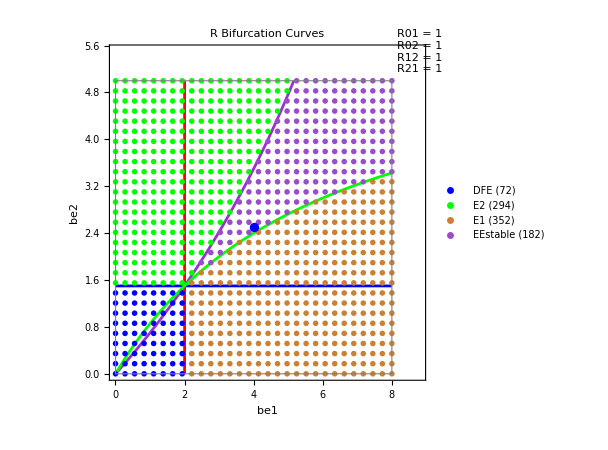

```mathematica
{plF,errors,res}=scanPar[RHS,var,par,p0val,plotInd,30,plot];plF
```

```mathematica
{plF,errors,res}=scanPar[RHS,var,par,p0val,{1,2},Automatic,plot,0.01,0.05];plot
```

Varying parameters at indices {1,2} with center values: {4,5/2}

Using range mode with step size 0.05...

Total points to scan: 16000

Scanning complete!

Found equilibrium types: {DFE (1200 points),E2 (5206 points),E1 (6379 points),EEstable (3215 points)}

Including 0 errors

Summary:

DFE | 1200 | 8%
E2 | 5206 | 33%
E1 | 6379 | 40%
EEstable | 3215 | 20%

-Graphics-

```mathematica
(*Fast parameter scanning using claP logic*)scanPar[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic]:=Module[{(*Parameter ranges and scanning*)β1,β2,β1min,β1max,β2min,β2max,stepSize,β1vals,β2vals,totalPoints,(*Results collection*)res,outcomes,outcomeCounts,(*Plotting and visualization*)finalPlot,plotData,betterColors,simpleTooltips,(*Mode detection*)useGridMode,β1Index,β2Index,β1Center,β2Center,(*Progress tracking*)progressVar,currentProgress,(*R curve variables*)R01F,R02F,R21F,R12F,rCurves,coPForR,(*Fast classification variables*)numpar,conPar,inP,sol,I1val,I2val,tol,currentType,errors,gridResults,nB1,nB2,jac,eigs,maxRealPart},(*Define better colors with old EE colors*)betterColors={RGBColor[0,0,1],(*Pure Blue for DFE*)RGBColor[0,1,0],(*Pure Green for E1*)RGBColor[0.8,0.5,0.2],(*Orange for E2*)RGBColor[0.6,0.3,0.8],(*Purple for EEstable*)RGBColor[1,0,0],(*Pure Red for EEunstable*)RGBColor[1.0,0.0,1.0](*Magenta for errors/NoSol*)};
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract parameter indices*)β1Index=If[Length[plotInd]>=1,plotInd[[1]],1];
β2Index=If[Length[plotInd]>=2,plotInd[[2]],2];
β1Center=p0val[[β1Index]];
β2Center=p0val[[β2Index]];
Print["Varying parameters at indices ",{β1Index,β2Index}," with center values: ",{β1Center,β2Center}];
If[useGridMode,(*GRID MODE*)Print["Using grid mode with ",gridRes,"×",gridRes," points..."];
β1min=Max[β1Center*(1-wRan),0.001];
β1max=β1Center*(1+wRan);
β2min=Max[β2Center*(1-hRan),0.001];
β2max=β2Center*(1+hRan);
β1vals=Table[β1min+(β1max-β1min)*k/(gridRes-1),{k,0,gridRes-1}];
β2vals=Table[β2min+(β2max-β2min)*k/(gridRes-1),{k,0,gridRes-1}];
stepSize="grid";,(*RANGE MODE*)Print["Using range mode with step size ",delta,"..."];
β1min=Max[β1Center*(1-wRan),0.001];
β1max=β1Center*(1+wRan);
β2min=Max[β2Center*(1-hRan),0.001];
β2max=β2Center*(1+hRan);
β1vals=Table[β1,{β1,β1min,β1max,delta}];
β2vals=Table[β2,{β2,β2min,β2max,delta}];
stepSize=delta;];
(*R curve preparation*)rCurves={};
If[R01=!=Automatic||R02=!=Automatic||R21=!=Automatic||R12=!=Automatic,coPForR=Thread[par->p0val];
coPForR=DeleteCases[coPForR,HoldPattern[par[[β1Index]]->_]|HoldPattern[par[[β2Index]]->_]];
If[R01=!=Automatic,R01F=R01/. coPForR;
AppendTo[rCurves,ContourPlot[R01F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Red,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R02=!=Automatic,R02F=R02/. coPForR;
AppendTo[rCurves,ContourPlot[R02F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Blue,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R21=!=Automatic,R21F=R21/. coPForR;
AppendTo[rCurves,ContourPlot[R21F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Green,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R12=!=Automatic,R12F=R12/. coPForR;
AppendTo[rCurves,ContourPlot[R12F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Orange,Thick,Opacity[0.8]],PlotPoints->30]]];];
totalPoints=Length[β1vals]*Length[β2vals];
Print["Total points to scan: ",totalPoints];
(*Initialize for fast scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
inP=Table[{var[[j]],1/Length[var]},{j,Length[var]}];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[β1Index]]=β1;
numpar[[β2Index]]=β2;
conPar=Thread[par->numpar];
(*Single FindRoot call with equal initial conditions*)sol=Quiet[FindRoot[RHS/. conPar,inP]];
If[Head[sol]===List,(*Extract I1,I2 and classify*){I1val,I2val}={I1,I2}/. sol;
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,(*Both strains present-check EE stability*)(jac=D[RHS,{var}]/. conPar/. sol;
eigs=Chop[Eigenvalues[jac]//N];
maxRealPart=Max[Re[eigs]];
If[maxRealPart<0,"EEstable","EEunstable"])];
res=Append[res,{N[β1],N[β2],currentType}];,(*FindRoot failed*)res=Append[res,{N[β1],N[β2],"NoSol"}];];,{β2,β2vals}];,{β1,β1vals}];
Print["Scanning complete!"];
(*Simple error detection for grid mode*)errors={};
If[useGridMode&&gridRes>2,gridResults=Table[Table[Null,{j,1,gridRes}],{i,1,gridRes}];
Do[Do[pos=Position[res,{β1vals[[i]],β2vals[[j]],_}];
If[Length[pos]>0,gridResults[[i,j]]=res[[pos[[1,1]],3]]];,{j,1,gridRes}];,{i,1,gridRes}];
Do[Do[If[gridResults[[i,j]]=!=Null,neighbors={};
If[i>1,AppendTo[neighbors,gridResults[[i-1,j]]]];
If[i<gridRes,AppendTo[neighbors,gridResults[[i+1,j]]]];
If[j>1,AppendTo[neighbors,gridResults[[i,j-1]]]];
If[j<gridRes,AppendTo[neighbors,gridResults[[i,j+1]]]];
neighbors=DeleteCases[neighbors,Null];
If[Length[neighbors]>=3&&Length[DeleteDuplicates[Join[{gridResults[[i,j]]},neighbors]]]>=4,AppendTo[errors,{β1vals[[i]],β2vals[[j]],gridResults[[i,j]]}];
pos=Position[res,{β1vals[[i]],β2vals[[j]],gridResults[[i,j]]}];
If[Length[pos]>0,res[[pos[[1,1]],3]]="error"];];];,{j,2,gridRes-1}];,{i,2,gridRes-1}];];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
Print["Found equilibrium types: ",Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>" points)",{i,1,Length[outcomes]}]];
Print["Including ",Length[errors]," errors"];
(*Create plot*)simpleTooltips=Table[Table[If[res[[j,3]]==outcomes[[i]],Tooltip[res[[j,1;;2]],outcomes[[i]]<>": β1="<>ToString[Round[res[[j,1]],0.01]]<>", β2="<>ToString[Round[res[[j,2]],0.01]]],Nothing],{j,1,Length[res]}],{i,1,Length[outcomes]}];
finalPlot=ListPlot[simpleTooltips,GridLines->Automatic,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>")",{i,1,Length[outcomes]}],AspectRatio->1,PlotLabel->"Parameter Space Analysis ("<>ToString[Length[res]]<>" points)",FrameLabel->{"Parameter "<>ToString[β1Index],"Parameter "<>ToString[β2Index]},LabelStyle->{FontSize->12,Black},ImageSize->450,PlotRange->{{β1min,β1max},{β2min,β2max}}];
(*Add R curves and overlays*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot,Sequence@@rCurves,Graphics[{EdgeForm[{Thick,Gray,Dashed}],FaceForm[None],Rectangle[{β1min,β2min},{β1max,β2max}],Blue,PointSize[0.015],Point[{{β1Center,β2Center}}]}],PlotRange->{{β1min*0.9,β1max*1.1},{β2min*0.9,β2max*1.1}}];,If[Length[rCurves]>0,finalPlot=Show[finalPlot,Sequence@@rCurves];];];
Print[Style["Summary:",FontWeight->Bold]];
Print[Grid[Table[{outcomes[[i]],outcomeCounts[[i]],ToString[Round[100.*outcomeCounts[[i]]/Length[res],1]]<>"%"},{i,1,Length[outcomes]}],Frame->All,Alignment->Left]];
{finalPlot,errors,res}];

(*Grid mode:scanPar[RHS,var,par,p0val,{1,2},30,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12]*)
(*Range mode:scanPar[RHS,var,par,p0val,{1,2},Automatic,plot,0.01,0.05,1.0,1.0,R01,R02,R21,R12]*)
plotInd={1,2};coP
p0val=par/.coP
{ploF,errors,res}=scanPar[RHS,var,par,p0val,plotInd,10(*,plot,.01*)];ploF
```

```mathematica
(*EXECUTE THIS FIRST:*)Clear[scan4TS]

(*Time Series Simulation-based multiple equilibrium scanning*)
scan4TS[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic,tMax_:100,nInitials_:8,steadyTol_:10^(-6)]:=Block[{bifP1,bifP2,bifP1min,bifP1max,bifP2min,bifP2max,stepSize,bifP1vals,bifP2vals,totalPoints,res,outcomes,outcomeCounts,finalPlot,plotData,betterColors,simpleTooltips,useGridMode,bifParIdx1,bifParIdx2,bifP1Center,bifP2Center,progressVar,currentProgress,R01F,R02F,R21F,R12F,rCurves,coPForR,numpar,conPar,initialConditions,tsol,finalValues,I1val,I2val,tol,currentType,errors,gridResults,I1Index,I2Index,solTol,allSols,uniqueSols,eqType,eqTypes,steadyStateReached,lastValues,deltaCheck,icSet,ic,finalTime,pos,rhsWithParams,rhsWithFunctions,odeSystem,initialCondSystem},(*Define colors including detailed coexistence categories*)betterColors={RGBColor[0,0,1],(*Pure Blue for DFE*)RGBColor[0,1,0],(*Pure Green for E1*)RGBColor[0.8,0.5,0.2],(*Orange for E2*)RGBColor[0.6,0.3,0.8],(*Purple for EE*)RGBColor[1,1,0],(*Yellow for EE-E1*)RGBColor[1,0.5,0],(*Red-Orange for EE-E2*)RGBColor[0,0.8,0.8],(*Cyan for E1-E2*)RGBColor[0.8,0,0.8],(*Magenta for EE-DFE*)RGBColor[0.5,0.8,0.5],(*Light Green for E1-DFE*)RGBColor[0.8,0.8,0.5],(*Light Orange for E2-DFE*)RGBColor[1.0,0.0,1.0](*Magenta for errors/NoSol*)};
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
Print["I1 at index ",I1Index,", I2 at index ",I2Index];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract bifurcation parameter indices from plotInd*)bifParIdx1=First[plotInd];
bifParIdx2=Last[plotInd];
bifP1Center=Part[p0val,bifParIdx1];
bifP2Center=Part[p0val,bifParIdx2];
Print["Varying bifurcation parameters at indices ",{bifParIdx1,bifParIdx2}," with center values: ",{bifP1Center,bifP2Center}];
Print["Time series simulation: tMax = ",tMax,", steadyTol = ",steadyTol,", nInitials = ",nInitials];
If[useGridMode,(*GRID MODE*)Print["Using grid mode with ",gridRes,"×",gridRes," points..."];
bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1min+(bifP1max-bifP1min)*k/(gridRes-1),{k,0,gridRes-1}];
bifP2vals=Table[bifP2min+(bifP2max-bifP2min)*k/(gridRes-1),{k,0,gridRes-1}];
stepSize="grid";,(*RANGE MODE*)Print["Using range mode with step size ",delta,"..."];
bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1,{bifP1,bifP1min,bifP1max,delta}];
bifP2vals=Table[bifP2,{bifP2,bifP2min,bifP2max,delta}];
stepSize=delta;];
(*R curve preparation*)rCurves={};
If[R01=!=Automatic||R02=!=Automatic||R21=!=Automatic||R12=!=Automatic,coPForR=Thread[par->p0val];
coPForR=DeleteCases[coPForR,HoldPattern[Part[par,bifParIdx1]->_]|HoldPattern[Part[par,bifParIdx2]->_]];
If[R01=!=Automatic,R01F=R01/. coPForR;
AppendTo[rCurves,ContourPlot[R01F==1,{Part[par,bifParIdx1],bifP1min,bifP1max},{Part[par,bifParIdx2],bifP2min,bifP2max},ContourStyle->Directive[Red,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R02=!=Automatic,R02F=R02/. coPForR;
AppendTo[rCurves,ContourPlot[R02F==1,{Part[par,bifParIdx1],bifP1min,bifP1max},{Part[par,bifParIdx2],bifP2min,bifP2max},ContourStyle->Directive[Blue,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R21=!=Automatic,R21F=R21/. coPForR;
AppendTo[rCurves,ContourPlot[R21F==1,{Part[par,bifParIdx1],bifP1min,bifP1max},{Part[par,bifParIdx2],bifP2min,bifP2max},ContourStyle->Directive[Green,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R12=!=Automatic,R12F=R12/. coPForR;
AppendTo[rCurves,ContourPlot[R12F==1,{Part[par,bifParIdx1],bifP1min,bifP1max},{Part[par,bifParIdx2],bifP2min,bifP2max},ContourStyle->Directive[Orange,Thick,Opacity[0.8]],PlotPoints->30]]];];
totalPoints=Length[bifP1vals]*Length[bifP2vals];
Print["Total points to scan: ",totalPoints];
(*Initialize for time series scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);(*Tolerance for comparing final states*)(*Create diverse initial condition sets*)initialConditions={};
(*Set 1:DFE-like (I1=I2≈0)*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 2:E1-like (I2≈0)*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 3:E2-like (I1≈0)*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Set 4:EE-like (both high)*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Additional random initial conditions*)Do[icSet=Table[RandomReal[{0.001,0.2}],{Length[var]}];
AppendTo[initialConditions,icSet];,{nInitials-4}];
Print["Created ",Length[initialConditions]," different initial conditions"];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP WITH TIME SERIES SIMULATION*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[bifParIdx1]]=bifP1;
numpar[[bifParIdx2]]=bifP2;
conPar=Thread[par->numpar];
(*Substitute parameters in RHS*)rhsWithParams=RHS/. conPar;
(*Transform variables to functions of t:S->S[t],I1->I1[t],etc*)rhsWithFunctions=rhsWithParams/. Thread[var->Through[var[t]]];
(*Run time series from different initial conditions*)allSols={};
Do[ic=initialConditions[[k]];
(*Construct ODE system*)odeSystem=MapThread[#1'[t]==#2&,{var,rhsWithFunctions}];
initialCondSystem=MapThread[#1[0]==#2&,{var,ic}];
(*Solve ODE system*)tsol=Quiet[NDSolve[Join[odeSystem,initialCondSystem],var,{t,0,tMax}]];
If[Length[tsol]>0&&tsol[[1]]=!=$Failed,(*Extract final values*)finalValues=Table[var[[j]][tMax]/. tsol[[1]],{j,1,Length[var]}];
(*Check if steady state was reached*)finalTime=0.9*tMax;
lastValues=Table[var[[j]][finalTime]/. tsol[[1]],{j,1,Length[var]}];
deltaCheck=Max[Abs[finalValues-lastValues]];
steadyStateReached=(deltaCheck<steadyTol);
If[steadyStateReached&&AllTrue[finalValues,#>=0&],AppendTo[allSols,finalValues]];];,{k,1,Length[initialConditions]}];
If[Length[allSols]>0,(*Find unique attractors (within tolerance)*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify based on number of unique attractors*)If[Length[uniqueSols]>1,(*Multiple attractors-classify each and determine coexistence type*)eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
(*Remove duplicates and sort to get consistent naming*)eqTypes=Sort[DeleteDuplicates[eqTypes]];
(*Determine coexistence type*)currentType=Which[ContainsAll[eqTypes,{"EE","E1"}]&&Length[eqTypes]==2,"EE-E1",ContainsAll[eqTypes,{"EE","E2"}]&&Length[eqTypes]==2,"EE-E2",ContainsAll[eqTypes,{"E1","E2"}]&&Length[eqTypes]==2,"E1-E2",ContainsAll[eqTypes,{"EE","DFE"}]&&Length[eqTypes]==2,"EE-DFE",ContainsAll[eqTypes,{"E1","DFE"}]&&Length[eqTypes]==2,"E1-DFE",ContainsAll[eqTypes,{"E2","DFE"}]&&Length[eqTypes]==2,"E2-DFE",True,"3-4 Fps" (*For 3+types or unexpected combinations*)];,(*Single attractor-classify by I1,I2 values*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];];
res=Append[res,{N[bifP1],N[bifP2],currentType}];,(*No steady states found or all simulations failed*)res=Append[res,{N[bifP1],N[bifP2],"NoSol"}];];,{bifP2,bifP2vals}];,{bifP1,bifP1vals}];
Print["Time series scanning complete!"];
(*Simple error detection for grid mode*)errors={};
If[useGridMode&&gridRes>2,gridResults=Table[Table[Null,{j,1,gridRes}],{i,1,gridRes}];
Do[Do[pos=Position[res,{bifP1vals[[i]],bifP2vals[[j]],_}];
If[Length[pos]>0,gridResults[[i,j]]=res[[pos[[1,1]],3]]];,{j,1,gridRes}];,{i,1,gridRes}];
Do[Do[If[gridResults[[i,j]]=!=Null,neighbors={};
If[i>1,AppendTo[neighbors,gridResults[[i-1,j]]]];
If[i<gridRes,AppendTo[neighbors,gridResults[[i+1,j]]]];
If[j>1,AppendTo[neighbors,gridResults[[i,j-1]]]];
If[j<gridRes,AppendTo[neighbors,gridResults[[i,j+1]]]];
neighbors=DeleteCases[neighbors,Null];
If[Length[neighbors]>=3&&Length[DeleteDuplicates[Join[{gridResults[[i,j]]},neighbors]]]>=4,AppendTo[errors,{bifP1vals[[i]],bifP2vals[[j]],gridResults[[i,j]]}];
pos=Position[res,{bifP1vals[[i]],bifP2vals[[j]],gridResults[[i,j]]}];
If[Length[pos]>0,res[[pos[[1,1]],3]]="error"];];];,{j,2,gridRes-1}];,{i,2,gridRes-1}];];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
Print["Found equilibrium types: ",Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>" points)",{i,1,Length[outcomes]}]];
Print["Including ",Length[errors]," errors"];
(*Create plot*)simpleTooltips=Table[Table[If[res[[j,3]]==outcomes[[i]],Tooltip[res[[j,1;;2]],outcomes[[i]]<>": "<>ToString[Part[par,bifParIdx1]]<>"="<>ToString[Round[res[[j,1]],0.01]]<>", "<>ToString[Part[par,bifParIdx2]]<>"="<>ToString[Round[res[[j,2]],0.01]]],Nothing],{j,1,Length[res]}],{i,1,Length[outcomes]}];
finalPlot=ListPlot[simpleTooltips,GridLines->Automatic,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>")",{i,1,Length[outcomes]}],AspectRatio->1,PlotLabel->"Time Series Bifurcation Analysis ("<>ToString[Length[res]]<>" points)",FrameLabel->{ToString[Part[par,bifParIdx1]],ToString[Part[par,bifParIdx2]]},LabelStyle->{FontSize->12,Black},ImageSize->450,PlotRange->{{bifP1min,bifP1max},{bifP2min,bifP2max}}];
(*Add R curves and overlays*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot,Sequence@@rCurves,Graphics[{EdgeForm[{Thick,Gray,Dashed}],FaceForm[None],Rectangle[{bifP1min,bifP2min},{bifP1max,bifP2max}],Blue,PointSize[0.015],Point[{{bifP1Center,bifP2Center}}]}],PlotRange->{{bifP1min*0.9,bifP1max*1.1},{bifP2min*0.9,bifP2max*1.1}}];,If[Length[rCurves]>0,finalPlot=Show[finalPlot,Sequence@@rCurves];];];
Print[Style["Summary:",FontWeight->Bold]];
Print[Grid[Table[{outcomes[[i]],outcomeCounts[[i]],ToString[Round[100.*outcomeCounts[[i]]/Length[res],1]]<>"%"},{i,1,Length[outcomes]}],Frame->All,Alignment->Left]];
{finalPlot,errors,res}];

(*Usage:*)
(*plotInd={1,2};*)
(*scan4TS[RHS,var,par,p0val,plotInd,15,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12,100,8,10^(-6)]*)
```

I1 at index 2, I2 at index 5

Varying bifurcation parameters at indices {1,2} with center values: {4,5/2}

Time series simulation: tMax = 100, steadyTol = 1/1000000, nInitials = 8

Using grid mode with 15×15 points...

StringForm::sfr: Item 2 requested in "`1` cannot be interpreted. The operator `2` requires a subscript with a variable specification." out of range; 1 items available.

Internal`LocalizedBlock::novar: {be1,be2,et1,et2,ga1,ga2,La,mu,si1,si2,«3»}⟦bifParIdx1⟧ cannot be interpreted. The operator `2` requires a subscript with a variable specification.

StringForm::sfr: Item 2 requested in "`1` cannot be interpreted. The operator `2` requires a subscript with a variable specification." out of range; 1 items available.

Internal`LocalizedBlock::novar: {be1,be2,et1,et2,ga1,ga2,La,mu,si1,si2,«3»}⟦bifParIdx1⟧ cannot be interpreted. The operator `2` requires a subscript with a variable specification.

StringForm::sfr: Item 2 requested in "`1` cannot be interpreted. The operator `2` requires a subscript with a variable specification." out of range; 1 items available.

General::stop: Further output of StringForm::sfr will be suppressed during this calculation.

Internal`LocalizedBlock::novar: {be1,be2,et1,et2,ga1,ga2,La,mu,si1,si2,«3»}⟦bifParIdx1⟧ cannot be interpreted. The operator `2` requires a subscript with a variable specification.

General::stop: Further output of Internal`LocalizedBlock::novar will be suppressed during this calculation.

Total points to scan: 225

Created 8 different initial conditions

Time series scanning complete!

Found equilibrium types: {DFE (10 points),NoSol (36 points),E2 (65 points),error (1 points),E1 (79 points),EE (34 points)}

Including 1 errors

Show::gcomb: Could not combine the graphics objects in ….

Summary:

DFE | 10 | 4%
NoSol | 36 | 16%
E2 | 65 | 29%
error | 1 | 0%
E1 | 79 | 35%
EE | 34 | 15%

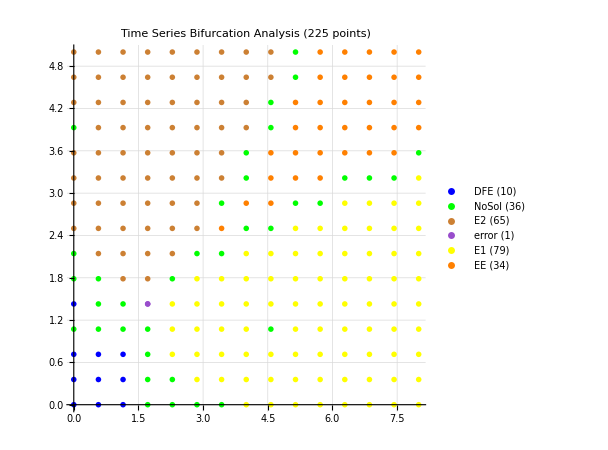
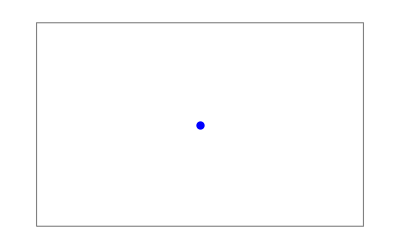
{Show[plot,-Graphics-,$Failed,$Failed,$Failed,$Failed,-Graphics-,PlotRange→{{0.0009,8.8},{0.0009,5.5}}],{{1.71507,1.42929,DFE}},{{0.001,0.001,DFE},{0.001,0.358071,DFE},{0.001,0.715143,DFE},{0.001,1.07221,NoSol},{0.001,1.42929,DFE},{0.001,1.78636,NoSol},{0.001,2.14343,NoSol},{0.001,2.5005,E2},{0.001,2.85757,E2},{0.001,3.21464,E2},{0.001,3.57171,E2},{0.001,3.92879,NoSol},{0.001,4.28586,E2},{0.001,4.64293,E2},{0.001,5.,E2},{0.572357,0.001,DFE},{0.572357,0.358071,DFE},{0.572357,0.715143,DFE},{0.572357,1.07221,NoSol},{0.572357,1.42929,NoSol},{0.572357,1.78636,NoSol},{0.572357,2.14343,E2},{0.572357,2.5005,E2},{0.572357,2.85757,E2},{0.572357,3.21464,E2},{0.572357,3.57171,E2},{0.572357,3.92879,E2},{0.572357,4.28586,E2},{0.572357,4.64293,E2},{0.572357,5.,E2},{1.14371,0.001,DFE},{1.14371,0.358071,DFE},{1.14371,0.715143,DFE},{1.14371,1.07221,NoSol},{1.14371,1.42929,NoSol},{1.14371,1.78636,E2},{1.14371,2.14343,E2},{1.14371,2.5005,E2},{1.14371,2.85757,E2},{1.14371,3.21464,E2},{1.14371,3.57171,E2},{1.14371,3.92879,E2},{1.14371,4.28586,E2},{1.14371,4.64293,E2},{1.14371,5.,E2},{1.71507,0.001,NoSol},{1.71507,0.358071,NoSol},{1.71507,0.715143,NoSol},{1.71507,1.07221,NoSol},{1.71507,1.42929,error},{1.71507,1.78636,E2},{1.71507,2.14343,E2},{1.71507,2.5005,E2},{1.71507,2.85757,E2},{1.71507,3.21464,E2},{1.71507,3.57171,E2},{1.71507,3.92879,E2},{1.71507,4.28586,E2},{1.71507,4.64293,E2},{1.71507,5.,E2},{2.28643,0.001,NoSol},{2.28643,0.358071,NoSol},{2.28643,0.715143,E1},{2.28643,1.07221,E1},{2.28643,1.42929,E1},{2.28643,1.78636,NoSol},{2.28643,2.14343,E2},{2.28643,2.5005,E2},{2.28643,2.85757,E2},{2.28643,3.21464,E2},{2.28643,3.57171,E2},{2.28643,3.92879,E2},{2.28643,4.28586,E2},{2.28643,4.64293,E2},{2.28643,5.,E2},{2.85779,0.001,NoSol},{2.85779,0.358071,E1},{2.85779,0.715143,E1},{2.85779,1.07221,E1},{2.85779,1.42929,E1},{2.85779,1.78636,E1},{2.85779,2.14343,NoSol},{2.85779,2.5005,E2},{2.85779,2.85757,E2},{2.85779,3.21464,E2},{2.85779,3.57171,E2},{2.85779,3.92879,E2},{2.85779,4.28586,E2},{2.85779,4.64293,E2},{2.85779,5.,E2},{3.42914,0.001,NoSol},{3.42914,0.358071,E1},{3.42914,0.715143,E1},{3.42914,1.07221,E1},{3.42914,1.42929,E1},{3.42914,1.78636,E1},{3.42914,2.14343,NoSol},{3.42914,2.5005,EE},{3.42914,2.85757,NoSol},{3.42914,3.21464,E2},{3.42914,3.57171,E2},{3.42914,3.92879,E2},{3.42914,4.28586,E2},{3.42914,4.64293,E2},{3.42914,5.,E2},{4.0005,0.001,E1},{4.0005,0.358071,E1},{4.0005,0.715143,E1},{4.0005,1.07221,E1},{4.0005,1.42929,E1},{4.0005,1.78636,E1},{4.0005,2.14343,E1},{4.0005,2.5005,NoSol},{4.0005,2.85757,EE},{4.0005,3.21464,NoSol},{4.0005,3.57171,NoSol},{4.0005,3.92879,E2},{4.0005,4.28586,E2},{4.0005,4.64293,E2},{4.0005,5.,E2},{4.57186,0.001,E1},{4.57186,0.358071,E1},{4.57186,0.715143,E1},{4.57186,1.07221,NoSol},{4.57186,1.42929,E1},{4.57186,1.78636,E1},{4.57186,2.14343,E1},{4.57186,2.5005,NoSol},{4.57186,2.85757,EE},{4.57186,3.21464,EE},{4.57186,3.57171,EE},{4.57186,3.92879,NoSol},{4.57186,4.28586,NoSol},{4.57186,4.64293,E2},{4.57186,5.,E2},{5.14321,0.001,E1},{5.14321,0.358071,E1},{5.14321,0.715143,E1},{5.14321,1.07221,E1},{5.14321,1.42929,E1},{5.14321,1.78636,E1},{5.14321,2.14343,E1},{5.14321,2.5005,E1},{5.14321,2.85757,NoSol},{5.14321,3.21464,EE},{5.14321,3.57171,EE},{5.14321,3.92879,EE},{5.14321,4.28586,EE},{5.14321,4.64293,NoSol},{5.14321,5.,NoSol},{5.71457,0.001,E1},{5.71457,0.358071,E1},{5.71457,0.715143,E1},{5.71457,1.07221,E1},{5.71457,1.42929,E1},{5.71457,1.78636,E1},{5.71457,2.14343,E1},{5.71457,2.5005,E1},{5.71457,2.85757,NoSol},{5.71457,3.21464,EE},{5.71457,3.57171,EE},{5.71457,3.92879,EE},{5.71457,4.28586,EE},{5.71457,4.64293,EE},{5.71457,5.,EE},{6.28593,0.001,E1},{6.28593,0.358071,E1},{6.28593,0.715143,E1},{6.28593,1.07221,E1},{6.28593,1.42929,E1},{6.28593,1.78636,E1},{6.28593,2.14343,E1},{6.28593,2.5005,E1},{6.28593,2.85757,E1},{6.28593,3.21464,NoSol},{6.28593,3.57171,EE},{6.28593,3.92879,EE},{6.28593,4.28586,EE},{6.28593,4.64293,EE},{6.28593,5.,EE},{6.85729,0.001,E1},{6.85729,0.358071,E1},{6.85729,0.715143,E1},{6.85729,1.07221,E1},{6.85729,1.42929,E1},{6.85729,1.78636,E1},{6.85729,2.14343,E1},{6.85729,2.5005,E1},{6.85729,2.85757,E1},{6.85729,3.21464,NoSol},{6.85729,3.57171,EE},{6.85729,3.92879,EE},{6.85729,4.28586,EE},{6.85729,4.64293,EE},{6.85729,5.,EE},{7.42864,0.001,E1},{7.42864,0.358071,E1},{7.42864,0.715143,E1},{7.42864,1.07221,E1},{7.42864,1.42929,E1},{7.42864,1.78636,E1},{7.42864,2.14343,E1},{7.42864,2.5005,E1},{7.42864,2.85757,E1},{7.42864,3.21464,NoSol},{7.42864,3.57171,EE},{7.42864,3.92879,EE},{7.42864,4.28586,EE},{7.42864,4.64293,EE},{7.42864,5.,EE},{8.,0.001,E1},{8.,0.358071,E1},{8.,0.715143,E1},{8.,1.07221,E1},{8.,1.42929,E1},{8.,1.78636,E1},{8.,2.14343,E1},{8.,2.5005,E1},{8.,2.85757,E1},{8.,3.21464,E1},{8.,3.57171,NoSol},{8.,3.92879,EE},{8.,4.28586,EE},{8.,4.64293,EE},{8.,5.,EE}}}

```mathematica
plotInd={1,2};
scan4TS[RHS,var,par,p0val,plotInd,15,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12,100,8,10^(-6)]
```